# Neural Logic

```mathematica
Get["neural-logic.m",Path->NotebookDirectory[]];
```

```mathematica
?neurallogic`*
```

## Utilities

```mathematica
HardPrediction[m_]:=Ordering[(With[{t=#[True]},If[MissingQ[t],0,t]]&)/@Counts/@m,-1]
HardTarget[t_]:=Flatten[Position[t,True]]
HardResults[hardPredictionTargetPairs_]:=Module[{results,accuracy},
results=Reverse[Sort[Counts[{HardPrediction[First[#]][[1]],HardTarget[Last[#]][[1]]}&/@hardPredictionTargetPairs]]];
accuracy=KeySelect[results,First[#]==Last[#]&];
{"Accuracy = "<>ToString[Total[accuracy]/Length[hardPredictionTargetPairs]*100.0]<>"%",results}
]
```

```mathematica
HardPrediction[{{True,False,False},{False,False,False},{True,True,False}}]
```

{3}

```mathematica
HardPrediction[{{True,False,False},{True,False,False},{False,False,False}}]
```

{2}

```mathematica
HardPrediction[{{True,True,False},{True,False,False},{True,True,True}}]
```

{3}

## Learn XOR

## Generate training data

```mathematica
numBooleanVariables=25;
Echo[2^numBooleanVariables];
bf=BooleanConvert[Xor[#1,#2,#3,#4,#5,#6,#7,#8,#9,#10,#11,#12,#13,#14,#15,#16,#17,#18,#19,#20,#21,#22,#23,#24,#25]&,"BooleanFunction"];
maxExamples=10000;
numClasses=2;
examples=Map[With[{x=RandomChoice[{0,1},numBooleanVariables]},Soften/@x->Soften[Boole[With[{r=bf@@x},{r,!r}]]]]&,Range[maxExamples]];
{trainData,testData}=[examples,"TestSetSize"->Scaled[0.2],"Shuffle"->True];
```

33554432

## Hard neural logic

### Create net

```mathematica
inputSize=Length[First[First[trainData]]];
```

```mathematica
{net,hardNet}=With[{classificationLayerSize=4*numClasses},
HardNeuralChain[{
HardNeuralNOR[inputSize,200],
HardNeuralNOR[200,classificationLayerSize],
HardNeuralPortLayer[classificationLayerSize,numClasses]
}]];
```

```mathematica
{net,hardNet}=With[{classificationLayerSize=4*numClasses},
HardNeuralChain[{
HardNeuralMajority[inputSize,200],
HardNeuralMajority[200,classificationLayerSize],
HardNeuralPortLayer[classificationLayerSize,numClasses]
}]];
```

```mathematica
softNet=AppendHardClassificationLoss[net]
```

NetGraph[<>]

### Train net

```mathematica
{trainedNet,resultsObject}=NetTrain[softNet,trainData,{"TrainedNet","ResultsObject"},
ValidationSet->{RandomSample[testData,UpTo[1000]],"Interval"->10},
LossFunction->"Loss",
Method->{"ADAM"},
TargetDevice->"GPU",
MaxTrainingRounds->20000];
```

```mathematica
trainedSoftNet=NetExtract[trainedNet,"NeuralLogicNet"]
```

NetChain[<>]

### Evaluate soft net

```mathematica
resultsObject["RoundMeasurements"]
softPredictionTargetPairs=[{trainedSoftNet[First[#]],Last[#]}&,testData];
hardenedPredictionTargetPairs=Harden[softPredictionTargetPairs];
MatrixForm/@Flatten[RandomSample[hardenedPredictionTargetPairs,5],1]/.{True->Style[True,Red]};
Column[HardResults[hardenedPredictionTargetPairs]]
```

<|Loss→0.249198|>

{(False | True | True | False
False | False | False | True),(True
False),(False | True | True | False
True | True | False | True),(False
True),(False | True | True | False
True | False | False | True),(False
True),(False | True | True | False
False | False | False | True),(False
True),(False | False | True | False
False | True | False | True),(False
True)}

Accuracy = 49.75%
<|{2,2}→586,{2,1}→565,{1,2}→440,{1,1}→409|>

### Evaluate hard net

```mathematica
hnf=HardNetFunction[hardNet,trainedSoftNet];
hardPredictionTargetPairs=[{hnf[Harden[First[#]]],Last[#]}&,testData];
Column[HardResults[hardenedPredictionTargetPairs]]
```

Accuracy = 49.75%
<|{2,2}→586,{2,1}→565,{1,2}→440,{1,1}→409|>

```mathematica
SpaceSaving[trainedSoftNet]
```

Soft net size = 27.232 kilobytes
Hard net size = 0.851 kilobytes
Saving factor = 32.

## Learn MNIST

## Generate training data

```mathematica
ConvertBinaryStringToList[s_String]:=ToExpression["{"<>StringInsert[s,",",Drop[Range[StringLength[s]],1]]<>"}"]
ConvertBinaryStringToImageData[s_String,{width_,height_}]:=ArrayReshape[ConvertBinaryStringToList[s],{width,height}]
MNISTExample[example_]:=(Soften/@ConvertBinaryStringToList[First[example]])->Last[example]
MNISTImageExample[example_,w_,h_]:=Image[ConvertBinaryStringToImageData[First[example],{w,h}],ImageSize->Tiny]->Last[example]
TargetClass[class_,numClasses_]:=Table[If[i==ToExpression[class]+1,1,0],{i,1,numClasses}]
```

```mathematica
first2Digits=12665;
first4Digits=24754;
data=Flatten[StringSplit/@Take[Import[FileNameJoin[{NotebookDirectory[],"data/mnist_data.csv"}]],first4Digits],1];
numClasses=Length[DeleteDuplicates[Last/@data]];
data=Map[First[#]->TargetClass[Last[#],numClasses]&,data];
```

```mathematica
MNISTImageExample[#,8,8]&/@RandomSample[data,8]
```

{-Graphics-→{0,1,0,0},-Graphics-→{1,0,0,0},-Graphics-→{0,0,0,1},-Graphics-→{0,1,0,0},-Graphics-→{1,0,0,0},-Graphics-→{1,0,0,0},-Graphics-→{1,0,0,0},-Graphics-→{0,1,0,0}}

```mathematica
{trainData,testData}=[MNISTExample/@data,"TestSetSize"->Scaled[0.8],"Shuffle"->True];
```

## Standard neural net

```mathematica
ConvertDataToClasses[data_]:=MapAt[First[Flatten[Position[#,1]]]-1&,data,{All,2}]
```

### Create net

```mathematica
net=With[{classificationLayerSize=numClasses},
NetChain[{
300,LogisticSigmoid,
classificationLayerSize,LogisticSigmoid,
SoftmaxLayer[]
},
"Output"->NetDecoder[{"Class",{"0","1","2","3"}}]
]];
```

### Train net

```mathematica
result=NetTrain[net,ConvertDataToClasses[trainData],All,
ValidationSet->{ConvertDataToClasses[RandomSample[testData,UpTo[1000]]],"Interval"->10},
Method->{"ADAM"},
TargetDevice->"GPU",
MaxTrainingRounds->2000];
```

### Evaluate net

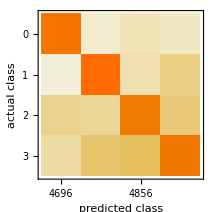
Classifier Measurements
Classifier method | Net
Number of test examples | 19803
Accuracy | (94.060.17) %
Accuracy baseline | (26.930.32) %
Geometric mean of probabilities | 0.448 ± 0.00065
Mean cross entropy | 0.803 ± 0.0014
Single evaluation time | 2.7 ms/example
Batch evaluation speed | 171. examples/ms
-Graphics- |

```mathematica
ClassifierMeasurements[result["TrainedNet"],ConvertDataToClasses[testData]]
```

```mathematica
Quantity[Length[Flatten[Normal/@Select[NetExtract[result["TrainedNet"],{All,"Weights"}],!MissingQ[#]&]]]*32.0/8000,"kilobytes"]
```

81.6 kB

## Hard neural logic

### Create net

```mathematica
inputSize=Length[First[First[trainData]]];
```

```mathematica
{net,hardNet}=With[{classificationLayerSize=16*numClasses},
HardNeuralChain[{
HardNeuralNAND[inputSize,300],
HardNeuralNAND[300,classificationLayerSize],
HardNeuralPortLayer[classificationLayerSize,numClasses]
}]];
```

```mathematica
{net,hardNet}=With[{classificationLayerSize=16*numClasses},
HardNeuralChain[{
HardNeuralNAND[inputSize,300],
HardNeuralMajority[300,classificationLayerSize],
HardNeuralPortLayer[classificationLayerSize,numClasses]
}]];
```

```mathematica
softNet=NetGraph[
<|
"NeuralLogicNet"->net,
"Loss"->HardClassificationLoss[]
|>,
{
"NeuralLogicNet"->"Loss"
}
]
```

NetGraph[<>]

### Train net

```mathematica
{trainedNet,resultsObject}=NetTrain[softNet,trainData,{"TrainedNet","ResultsObject"},
ValidationSet->{RandomSample[testData,UpTo[1000]],"Interval"->10},
LossFunction->{"Loss"},
Method->{"ADAM"},
TargetDevice->"GPU",
MaxTrainingRounds->2000];
```

```mathematica
trainedSoftNet=NetExtract[trainedNet,"NeuralLogicNet"]
```

NetChain[<>]

### Evaluate soft net

```mathematica
resultsObject["RoundMeasurements"]
softPredictionTargetPairs=[{trainedSoftNet[First[#]],Last[#]}&,testData];
hardenedPredictionTargetPairs=Harden[softPredictionTargetPairs];
Column[HardResults[hardenedPredictionTargetPairs]]
```

<|Loss→0.133734,ErrorRate→0.0380609|>

Accuracy = 89.7591%
<|{2,2}→4659,{4,4}→4618,{1,1}→4404,{3,3}→4094,{4,2}→685,{4,3}→481,{4,1}→175,{3,4}→156,{3,1}→111,{2,3}→107,{1,3}→89,{2,4}→81,{1,4}→70,{3,2}→56,{2,1}→13,{1,2}→4|>

```mathematica
MatrixForm/@Flatten[RandomSample[hardenedPredictionTargetPairs,5],1]/.{True->Style[True,Red]}
```

{(False | False | False | False | False | False | False | False | False | False | False | False | False | False | False | False
False | True | True | True | True | True | True | True | True | True | True | True | True | False | True | False
False | False | False | False | True | False | False | False | False | False | False | False | False | False | False | False
False | False | False | False | False | False | False | False | False | False | False | False | False | False | False | False),(False
True
False
False),(False | False | False | False | False | False | False | False | False | False | False | False | False | False | False | False
False | False | False | False | False | False | False | False | False | False | False | False | False | False | False | False
True | True | True | False | True | True | False | True | True | False | False | False | True | True | False | True
False | False | False | False | False | False | False | False | False | False | False | False | False | False | False | False),(False
False
True
False),(False | False | False | False | False | False | False | False | False | False | False | False | False | False | True | False
True | False | True | True | True | False | True | False | False | True | True | True | True | False | True | True
False | False | True | False | False | False | False | False | False | False | True | False | True | False | True | False
False | False | False | False | False | False | False | False | False | True | True | True | False | False | True | True),(False
True
False
False),(True | False | False | True | True | True | True | False | True | True | True | True | False | True | True | True
False | False | False | False | False | False | False | False | False | False | False | False | False | False | False | False
False | False | False | False | False | False | False | False | False | False | False | False | False | False | False | False
False | False | False | False | False | True | False | False | False | True | False | True | False | False | False | False),(True
False
False
False),(True | True | True | True | True | True | True | False | True | True | True | True | True | True | True | True
False | False | False | False | False | False | False | False | False | False | False | False | False | False | False | False
False | False | False | False | False | False | False | False | False | False | False | False | False | True | False | False
False | False | False | False | False | False | False | False | False | False | False | False | False | False | False | False),(True
False
False
False)}

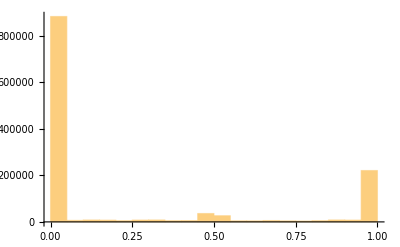

```mathematica
Histogram[Flatten[First/@softPredictionTargetPairs],PlotRange->All]
```

```mathematica
Histogram[Flatten[ExtractWeights[trainedSoftNet]],PlotRange->All]
```

-Graphics-

### Evaluate hard net

```mathematica
hnf=HardNetFunction[hardNet,trainedSoftNet];
hardPredictionTargetPairs=[{hnf[Harden[First[#]]],Last[#]}&,testData];
Column[HardResults[hardenedPredictionTargetPairs]]
```

Accuracy = 87.2898%
<|{2,2}→4931,{4,4}→4304,{1,1}→4247,{3,3}→3804,{4,3}→423,{2,3}→409,{3,4}→357,{4,2}→299,{4,1}→216,{2,4}→210,{1,3}→189,{3,1}→173,{3,2}→102,{1,4}→94,{2,1}→44,{1,2}→1|>

```mathematica
SpaceSaving[trainedSoftNet]
```

Soft net size = 412.8 kilobytes
Hard net size = 12.9 kilobytes
Saving factor = 32.

## Approximate neural logic

### Create net

```mathematica
softNet=NetChain[{
NeuralAND[Length[First[First[trainData]]],75],
NeuralNOT[75],
NeuralAND[75,numClasses]
}];
```

```mathematica
softNet=InitializeNeuralLogicNet[softNet];
```

### Train net

```mathematica
{trainedNet,resultsObject}=NetTrain[softNet,trainData,{"TrainedNet","ResultsObject"},
ValidationSet->{RandomSample[testData,UpTo[1000]],"Interval"->10},
(*LossFunction->CrossEntropyLossLayer["Binary"],*)
LossFunction->MeanSquaredLossLayer[],
Method->{"ADAM"},
TargetDevice->"GPU",
MaxTrainingRounds->2000];
```

### Evaluate

```mathematica
resultsObject["RoundMeasurements"]
```

<|Loss→0.0804611|>

```mathematica
randomTestSample=RandomSample[testData,UpTo[200]];
softPredictionTargetPairs=[{trainedNet[First[#]],Last[#]}&,randomTestSample];
RandomSample[softPredictionTargetPairs,10]
```

{{{4.33337×10^-6,0.0894224,0.013937,2.13952×10^-8},{0,1,0,0}},{{0.450201,0.000940334,0.0058358,0.00133961},{1,0,0,0}},{{0.00388923,0.223233,0.0197837,0.944495},{0,0,0,1}},{{0.855183,0.0121957,0.0058358,0.0109512},{1,0,0,0}},{{0.015117,0.622378,1.21929×10^-7,0.0143295},{0,1,0,0}},{{0.00197673,0.54449,0.013937,0.328144},{0,1,0,0}},{{0.999999,0.0661812,0.0587838,0.0196368},{1,0,0,0}},{{0.546544,0.00542415,0.0403483,0.0173441},{1,0,0,0}},{{0.846613,0.0121957,0.010335,0.0163952},{1,0,0,0}},{{0.395582,0.236313,0.0313908,0.90628},{1,0,0,0}}}

## Notes

```mathematica
Get["neural-logic.m",Path->NotebookDirectory[]];
```

```mathematica
HardClassificationLoss[]
```

NetGraph[<>]

```mathematica
hcl=HardeningClassificationLoss[1]
```

NetGraph[<>]

```mathematica
hcl[{{0.1,0.6,0.1},{0.9, 0.1,0.7},{0.6,0.6,0.9}}]
```

2.02831

```mathematica
hcl[{{0.1,0.6,0.1},{0.9, 0.1,0.7},{0.6,0.6,0.4}}]
```

1.76309

```mathematica
hcl[{{0.1,0.6,0.1},{0.9, 0.3,0.45},{0.8,0.45,0.49}}]
```

1.17822

```mathematica
hcl[{{0.4,0.6,0.4},{0.9, 0.05,0.05},{0.8,0.1,0.1}}]
```

1.11709

```mathematica
SoftClassificationLoss[]
```

NetGraph[<>]

```mathematica
g[x_List]:=Total[#-0.5&/@x]
```

```mathematica
f[x_List]:=Variance[Abs[#-0.5]&/@x]
```

```mathematica
With[{x={0.2,0.6,0.8,0.7}},{f[x],g[x]}]
```

{0.00916667,0.3}

```mathematica
With[{x={0.2,0.2,0.8,0.8}},{f[x],g[x]}]
```

{2.05433×10^-33,1.11022×10^-16}

```mathematica
With[{x={0.2,0.2,0.8,0.8,0.8}},{f[x],g[x]}]
```

{1.54074×10^-33,0.3}

```mathematica
Variance[{x1,x2,x3}]
```

1/6 ((2 x1-x2-x3) Conjugate[x1]+(-x1+2 x2-x3) Conjugate[x2]+(-x1-x2+2 x3) Conjugate[x3])

```mathematica
hcl=HardClassificationLoss[3,4]
```

NetGraph[<>]

```mathematica
hcl[<|"Input"->{{0.1,0.2,0.3,0.4},{0.49,0.6,0.7,0.8},{0.9,0.2,0.6,0.4}},"Target"->{1,0,0}|>]
```

1.93491

```mathematica
hcl[<|"Input"->{{0.1,0.2,0.3,0.4},{0.3,0.7,0.53,0.8},{0.9,0.2,0.6,0.6}},"Target"->{0,1,0}|>]
```

0.541378

```mathematica
hcl[<|"Input"->{{0.1,0.2,0.3,0.4},{0.3,0.6,0.7,0.8},{0.9,0.2,0.6,0.6}},"Target"->{0,0,1}|>]
```

0.558937

```mathematica
hcl[<|"Input"->{{0.3,0.6,0.7,0.8},{0.9,0.2,0.6,0.6},{0.1,0.2,0.3,0.4}},"Target"->{0,0,1}|>]
```

1.9327

```mathematica
hcl[<|"Input"->{{0.3,0.4,0.7,0.8},{0.9,0.2,0.6,0.6},{0.1,0.2,0.3,0.4}},"Target"->{0,0,1}|>]
```

1.75997

```mathematica
hcl[<|"Input"->{{0.91,0.81,0.6,0.81},{0.4,0.2,0.6,0.6},{0.1,0.2,0.3,0.4}},"Target"->{1,0,0}|>]
```

0.234472

```mathematica
hcl[<|"Input"->{{0.91,0.81,0.9,0.81},{0.1,0.2,0.1,0.2},{0.1,0.2,0.3,0.2}},"Target"->{1,0,0}|>]
```

0.0028015